```mathematica
X=3943;
n=1461;
```

```mathematica
z=InverseCDF[NormalDistribution[],0.975];
f=Function[m,m*X/n];
fL=Function[m,f[m]-z √(m*f[m](1/m+1/n))];
fR=Function[m,f[m]+z √(m*f[m](1/m+1/n))];
```

```mathematica
N[{f[365],fL[365],fR[365]}]
```

{985.075,916.304,1053.85}

```mathematica
Mean[{985.0752908966462,916.3038565413964,1053.846725251896}]
```

985.075

```mathematica
data1=TimeSeries[Table[f[m],{m,1,365}],{"Jan 1,2019"}];
data2=TimeSeries[Table[fL[m],{m,1,365}],{"Jan 1,2019"}];
data3=TimeSeries[Table[fR[m],{m,1,365}],{"Jan 1,2019"}];
```

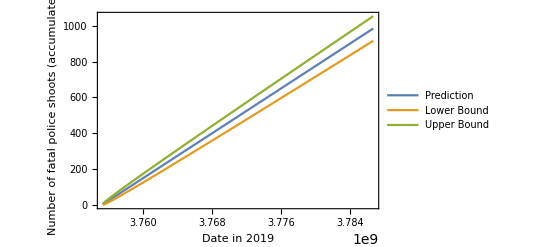

```mathematica
fig=DateListPlot[
{data1,data2,data3},
PlotLegends->{"Prediction","Lower Bound","Upper Bound"},
Frame->{True,True,False,False},
FrameLabel->{"Date in 2019","Number of fatal police shoots (accumulated)"}
]
Export["q7.eps",fig];
```

```mathematica
data=Import["policeshootings2019.json"];
dates="date"/.data;
days=DayCount[{2019,1,1},Keys[Counts[dates]][[-1]],"Day"]+1;
```

```mathematica
data1=TimeSeries[Table[f[m],{m,1,days}],{"Jan 1,2019"}];
data2=TimeSeries[Table[fL[m],{m,1,days}],{"Jan 1,2019"}];
data3=TimeSeries[Table[fR[m],{m,1,days}],{"Jan 1,2019"}];
data4=Accumulate[TimeSeries[Tally[dates]]];
```

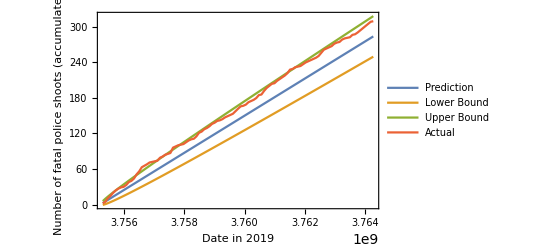

```mathematica
fig=DateListPlot[
{data1,data2,data3,data4},
PlotLegends->{"Prediction","Lower Bound","Upper Bound","Actual"},
Frame->{True,True,False,False},
FrameLabel->{"Date in 2019","Number of fatal police shoots (accumulated)"}
]
Export["q7-actual.eps",fig];
```